## Parameters

```mathematica
wd=NotebookDirectory[];
SetDirectory[wd];
(*Read parameter file into conf*)
readConf[filename_]:=Module[{res={},i,rawF,Ln,chk},
rawF=ReadList[filename,"String"];
Print[Length[rawF]];
For[i=1,i<=Length[rawF],++i,
If[rawF[[i]]=={},Continue[]];
If[StringTake[rawF[[i]],1]=="#",Continue[]];
Ln=StringSplit[rawF[[i]]];
If[NumericQ[ToExpression[Ln[[2]]]],AppendTo[res,Ln[[1]]->ToExpression[Ln[[2]]]],AppendTo[res,Ln[[1]]->Ln[[2]]]];
];
Association[res]
];
(*Parameters can be called same as in py*)
conf=readConf["../params"];
StateList={"1S"};
```

97

```mathematica
conf
```

<|L→50,dt→1.,T→0.3,tFn→80,NY→100000,Nbb→1,pSampleType→0,UniPMax→10,pSampSig→0.2,MatrElems→0,qRGtype→1,ECut→40,prCut→22,NPts→400,ExportRates→True,NXPart→16,NThreads→14,HydroMode→0,HPts→20,doRecom→1,doDisso→1,Mb→4.65,M1S→9.091,M2S→10.023,E1S→0.20925,E2S→0.723,bsig→0.01,Ysig→0.02,alphaS→0.3,CF→1.3333333333333333333,NC→3,gs→0.75,Ch→0,rateFile→bottom_rates_2d.tsv,boop→gleep|>

```mathematica
hbarc=0.1973;
```

```mathematica
Mnl[En_]:=2*conf["Mb"]-En;
```

### Matrix Elements

```mathematica
aB[st_]:=2/(conf["alphaS"]*conf["CF"]*conf["M"<>"b"]);
(*Matrix Elements*)
MOvLp[prel_,st_]:=Piecewise[{{
(((2^10)(Pi)(aB[st]^7)(prel^2)))/((1+(aB[st]^2)(prel^2))^6),st=="1S"},
{
((2^21)(Pi)(aB[st]^7)(prel^2)(1-2(aB[st]^2)(prel^2))^2)/((1+4(aB[st]^2)(prel^2))^8),st=="2S"}}];
```

### Thermal Distributions

```mathematica
fBM[p_,M_,T_]:=(p^2)Exp[-Sqrt[M^2+p^2]/T];(*Boltzmann mag. dist*)
fBMNorm[st_]:=1/((1/(2Pi^2))(conf["M"<>st]^2)*conf["T"]*BesselK[2,conf["M"<>st]/conf["T"]])*((4Pi)/(2Pi)^3);(*Normalization Const for ^^^*)
```

### Lorentz Boosts

```mathematica
Λ[v_]:={{(1/Sqrt[1-v.v]),-(1/Sqrt[1-v.v])v[[1]],-(1/Sqrt[1-v.v])v[[2]],-(1/Sqrt[1-v.v])v[[3]]},
{-(1/Sqrt[1-v.v])v[[1]],1+((1/Sqrt[1-v.v])-1)(v[[1]]^2)/(v.v),((1/Sqrt[1-v.v])-1)v[[1]]*v[[2]]/(v.v),((1/Sqrt[1-v.v])-1)v[[1]]*v[[3]]/(v.v)},
{-(1/Sqrt[1-v.v])v[[2]],((1/Sqrt[1-v.v])-1)v[[2]]*v[[1]]/(v.v),1+((1/Sqrt[1-v.v])-1)(v[[2]]^2)/(v.v),((1/Sqrt[1-v.v])-1)v[[2]]*v[[3]]/(v.v)},
{-(1/Sqrt[1-v.v])v[[3]],((1/Sqrt[1-v.v])-1)v[[3]]*v[[1]]/(v.v),((1/Sqrt[1-v.v])-1)v[[3]]*v[[2]]/(v.v),1+((1/Sqrt[1-v.v])-1)(v[[3]]^2)/(v.v)}};
```

```mathematica
MatrixForm[Λ[{Subscript[v, x],Subscript[v, y],Subscript[v, z]}]]
```

(1/(√(1-v_x^2-v_y^2-v_z^2)) | -v_x/(√(1-v_x^2-v_y^2-v_z^2)) | -v_y/(√(1-v_x^2-v_y^2-v_z^2)) | -v_z/(√(1-v_x^2-v_y^2-v_z^2))
-v_x/(√(1-v_x^2-v_y^2-v_z^2)) | 1+(v_x^2 (-1+1/(√(1-v_x^2-v_y^2-v_z^2))))/(v_x^2+v_y^2+v_z^2) | (v_x v_y (-1+1/(√(1-v_x^2-v_y^2-v_z^2))))/(v_x^2+v_y^2+v_z^2) | (v_x v_z (-1+1/(√(1-v_x^2-v_y^2-v_z^2))))/(v_x^2+v_y^2+v_z^2)
-v_y/(√(1-v_x^2-v_y^2-v_z^2)) | (v_x v_y (-1+1/(√(1-v_x^2-v_y^2-v_z^2))))/(v_x^2+v_y^2+v_z^2) | 1+(v_y^2 (-1+1/(√(1-v_x^2-v_y^2-v_z^2))))/(v_x^2+v_y^2+v_z^2) | (v_y v_z (-1+1/(√(1-v_x^2-v_y^2-v_z^2))))/(v_x^2+v_y^2+v_z^2)
-v_z/(√(1-v_x^2-v_y^2-v_z^2)) | (v_x v_z (-1+1/(√(1-v_x^2-v_y^2-v_z^2))))/(v_x^2+v_y^2+v_z^2) | (v_y v_z (-1+1/(√(1-v_x^2-v_y^2-v_z^2))))/(v_x^2+v_y^2+v_z^2) | 1+(v_z^2 (-1+1/(√(1-v_x^2-v_y^2-v_z^2))))/(v_x^2+v_y^2+v_z^2))

```mathematica
(*Utility functions*)
vFg[γ_]:=Sqrt[1-(1/γ^2)];
gFv[v_]:=1/Sqrt[1-(v^2)];
gFp[p_,st_]:=1/Sqrt[1-(p/Sqrt[p^2+conf["M"<>st]^2])^2];
```

```mathematica
Fourb[p3_]:={Sqrt[conf["Mb"]^2+(p3.p3)],p3[[1]],p3[[2]],p3[[3]]};
FourY[p3_,st_]:={Sqrt[conf["M"]^2+(p3.p3)],p3[[1]],p3[[2]],p3[[3]]};
```

## Other

```mathematica
-(0.4^2)conf["Mb"]/9
```

-0.0826667

### p_rel distribution

```mathematica
(*Get boltzmann inverse CDF*)
fBMCDFb=Table[{(fBMNorm["b"])*(NIntegrate[fBM[pi,conf["Mb"],conf["T"]],{pi,0,p}]),p},{p,0,conf["prCut"],conf["prCut"]/conf["NPts"]}];
fBMiCDFbint=Interpolation[fBMCDFb];
Plot[fBMiCDFbint[x],{x,0,1}]
```

Interpolation::inddp: The point 1. in dimension 1 is duplicated.

General::stop: Further output of Interpolation::inddp will be suppressed during this calculation.

-Graphics-

```mathematica
(*Sample a list of relative boosted momentums sampled from boltzmann dist*)
SampPb:=fBMiCDFbint[RandomReal[]]*RandomPoint[Sphere[],1][[1]];
SampPbM:=fBMiCDFbint[RandomReal[]];
SampPrel[n_]:=Module[{j,pcm,vcm,cmBpr,res,p1,p2},
res={};
For[j=1,j<=n,++j,
{p1,p2}={SampPb,SampPb};
pcm=p1+p2;
vcm=pcm/Sqrt[((2conf["Mb"])^2)+(pcm^2)];
cmBpr=(1/2)((Λ[vcm].Join[{Sqrt[(p1.p1)+(conf["Mb"])^2]},p1])[[2;;]]-(Λ[vcm].Join[{Sqrt[(p2.p2)+(conf["Mb"])^2]},p2])[[2;;]]);
AppendTo[res,Norm[cmBpr]];
];
res
];
SampPrelb:=Module[{p1,p2,pcm,vcm,cmBpr},
{p1,p2}={SampPb,SampPb};
pcm=p1+p2;
vcm=pcm/Sqrt[((2conf["Mb"])^2)+(pcm^2)];
cmBpr=(1/2)((Λ[vcm].Join[{Sqrt[(p1.p1)+(conf["Mb"])^2]},p1])[[2;;]]-(Λ[vcm].Join[{Sqrt[(p2.p2)+(conf["Mb"])^2]},p2])[[2;;]]);
Norm[cmBpr]
];
```

```mathematica
prDSamp=SampPrel[5000];
Show[Histogram[prDSamp,50,PDF],Plot[PDF[SmoothKernelDistribution[prDSamp],p],{p,0,5}]]
prDist=SmoothKernelDistribution[prDSamp];
prDistf[p_]:=PDF[prDist,p];
```

Interpolation::inddp: The point 1. in dimension 1 is duplicated.

General::stop: Further output of Interpolation::inddp will be suppressed during this calculation.

$Aborted

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[prDSamp].

Histogram::ldata: prDSamp is not a valid dataset or list of datasets.

Show::gcomb: Could not combine the graphics objects in Show[Histogram[prDSamp,50,PDF],].

Show[Histogram[prDSamp,50,PDF],-Graphics-]

SmoothKernelDistribution::invldd: The input data SmoothKernelDistribution[prDSamp] should be a vector or a matrix of real numbers or a valid TemporalData object.

```mathematica
(fBMNorm["1S"]/(2Pi)^3)*(NIntegrate[fBM[pi,conf["M1S"],conf["T"]],{pi,0,Infinity}]*4Pi)
```

0.0506606

```mathematica
NIntegrate[fBM[pi,conf["M1S"],conf["T"]],{pi,0,Infinity}]*fBMNorm["1S"]
```

1.

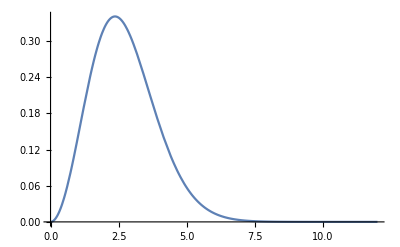

```mathematica
Plot[fBMNorm["1S"]*fBM[p,conf["M1S"],conf["T"]],{p,0,conf["prCut"]}]
```

```mathematica
pts=RandomPoint[Sphere[],10000];
Graphics3D[{PointSize[Tiny],Point[pts]},Boxed->False]
```

-Graphics3D-

```mathematica
pts
```

```mathematica
{{1,2},{1,2},{3,4}}*{1,0,2}
```

{{1,2},{0,0},{6,8}}

```mathematica
{1,2,3,4}[[2;;]]
```

{2,3,4}

```mathematica
tofm[dat_]:=Transpose[{dat[[All,1]]*hbarc,dat[[All,2]]}];
```

## Dissociation Channels

### Real Gluon Absorption

```mathematica
(* RGA rate *)
ΓRGAint[st_,q_,γ_]:=(2*conf["alphaS"]*conf["M"<>"b"]*conf["T"]/(9(Pi^2)(γ^2)*Sqrt[1-(1/γ^2)]))*(q^2)Sqrt[conf["M"<>"b"](q-conf["E"<>st])]Log[((1-Exp[-γ(1+Sqrt[1-(1/γ^2)])q/conf["T"]])/(1-Exp[-γ(1-Sqrt[1-(1/γ^2)])q/conf["T"]]))]*MOvLp[Sqrt[conf["M"<>"b"](q-conf["E"<>st])],st];
(* Integrate out q for (directly)sampled p-points~γ-points *)
ΓRGA1S=Table[{p,NIntegrate[ΓRGAint["1S",q,1/Sqrt[1-(p/Sqrt[p^2+conf["M"<>"1S"]^2])^2]],{q,conf["E"<>"1S"],Infinity}]},{p,0.1,conf["prCut"],0.01}];
```

```mathematica
Plot3D[ΓRGAint["1S",q,gFp[p,"1S"]],{q,0,conf["ECut"]*conf["E1S"]},{p,0,conf["prCut"]},PlotPoints->50,AxesLabel->{"q","p","ΓRGA"}]
```

-Graphics3D-

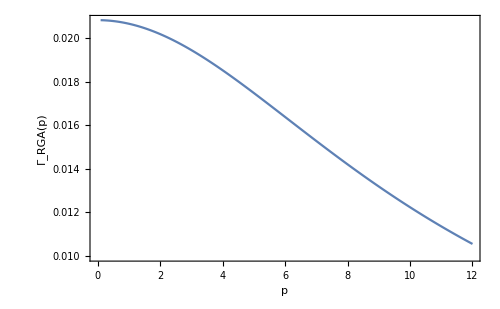

```mathematica
ListPlot[ΓRGA1S,Joined->True,PlotRange->All,Frame->True,FrameLabel->{{"Γ_RGA(p)",""},{"p","RGA marginal rate"}},FrameStyle->Directive[Black,FontSize->12],ImageSize->500]
```

```mathematica
(*Sample Dissociation Expectation (1S)*)
```

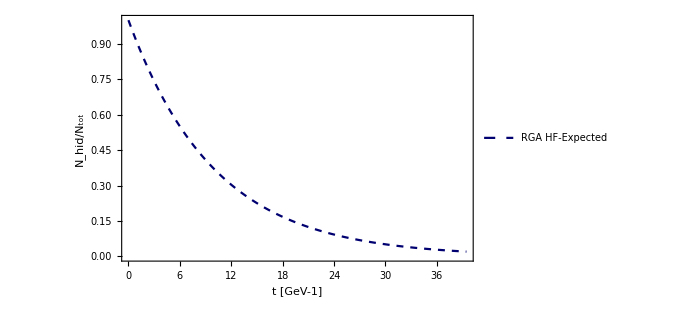

```mathematica
RGAsampInterp=Interpolation[ΓRGA1S];
If[conf["pSampleType"]==0,
RGAsampHF={{0,1}};
RGAsampDist=(1)(1/NIntegrate[fBM[p,conf["M1S"],conf["T"]],{p,0,Infinity}])*Table[fBM[pi,conf["M1S"],conf["T"]],{pi,0,conf["prCut"],0.05}];
ΓRGAresamp=RGAsampInterp/@Table[pi,{pi,0,conf["prCut"],0.05}]//Quiet;
(*Iterate application of += -(Ni*fB[p]*ΓRGA[p])*)
For[i=1,i<=conf["tFn"],++i,
RGAsampDist=RGAsampDist-(RGAsampDist*ΓRGAresamp*conf["dt"]);
AppendTo[RGAsampHF,{i*conf["dt"],Total[RGAsampDist]*(conf["prCut"]/(Length[RGAsampDist]-1))}];
];
];
If[conf["pSampleType"]==2,
RGAsampHF=Table[{i*conf["dt"],Exp[-RGAsampInterp[conf["UniPMax"]]*i*conf["dt"]]},{i,0,conf["tFn"]}];
];
RGAExpectPlot=ListPlot[tofm[RGAsampHF],Frame->True,FrameLabel->{{"N_hid/N_tot",""},{"t [GeV-1]","RGA hidden fraction expectation"}},FrameStyle->Directive[Black,FontSize->12],ImageSize->500,Joined->True,PlotStyle->Directive[{Darker[Darker[Blue]],Dashed}],PlotLegends->{"RGA HF-Expected"}]
```

## Recombination Channels

### Real Gluon Radiation (RGR)

```mathematica
ΓRGRsum[st_,x_,q_,γ_]:=Piecewise[{{((3/4)/conf["NC"]^2)(Exp[-(x^2)/(2*aB[st]^2)]/((2Pi*aB[st]^2)^(3/2)))(8/9)conf["alphaS"]*(q^3)(2+(conf["T"]/(γ*vFg[γ]*q))Log[(1-Exp[-γ(1+vFg[γ])q/conf["T"]])/(1-Exp[-γ(1-vFg[γ])q/conf["T"]])])*MOvLp[Sqrt[conf["Mb"](q-conf["E"<>st])],st],γ>1},{((3/4)/conf["NC"]^2)(Exp[-(x^2)/(2aB[st]^2)]/(2Pi*aB[st]^2)^(3/2))(8/9)conf["alphaS"](q^3)*(2+(2/(Exp[q/conf["T"]]-1)))*MOvLp[Sqrt[conf["Mb"](q-conf["E"<>st])],st],γ==1}}];
(*q maps to prel and γ->vcm*)
```

```mathematica
Plot3D[{ΓRGRsum["1S",x,(conf["E1S"]+pr^2/conf["Mb"]),gFp[0,"1S"]],ΓRGRsum["1S",x,(conf["E1S"]+pr^2/conf["Mb"]),gFp[2,"1S"]],ΓRGRsum["1S",x,(conf["E1S"]+pr^2/conf["Mb"]),gFp[20,"1S"]]},{x,0,3.5},{pr,0.1,conf["prCut"]/2},PlotStyle->{Directive[{Red,Opacity[0.3]}],Directive[{Green,Opacity[0.3]}],Directive[{Blue,Opacity[0.3]}]},PlotRange->All,PlotPoints->100,ScalingFunctions->"Linear"]
```

-Graphics3D-

-Graphics3D-

```mathematica
AgRGR[st_,q_,γ_]:=(8/9)conf["alphaS"]*(q^3)(2+(conf["T"]/(γ*vFg[γ]*q))Log[(1-Exp[-γ(1+vFg[γ])q/conf["T"]])/(1-Exp[-γ(1-vFg[γ])q/conf["T"]])])*MOvLp[Sqrt[conf["M"<>st](q-conf["E"<>st])],st]; (*1911.08500-4.123*)
```

```mathematica
(*AvgRateRGR[st_,γ_]:=(6)NIntegrate[(conf["Nbb"]/(conf["L"]^3))]*)
```

```mathematica
(*Integrate prelDist*ΓRGRsum*dprel and intepolate  + mapped γ->p *)
(*RGR1Sinterp=Interpolation[Table[{{x,p},NIntegrate[prDistf[pr]*ΓRGRsum["1S",x,(conf["E1S"]+pr^2/conf["Mb"]),gFp[p,"1S"]],{pr,0,conf["prCut"]}]},{x,0,conf["L"]/conf["NXPart"],conf["L"]/conf["NPts"]},{p,0,conf["prCut"],conf["prCut"]/conf["NPts"]}]];
Plot3D[RGR1Sinterp[x,p],{x,0,conf["L"]/conf["NXPart"]},{p,0,conf["prCut"]}]*)
```

```mathematica
(*MC Integration of ΓRGRsum -> marginal[γ->p]*)
MCNum=10000;
(*SampRGRxprel[γ_,st_]:=Module[{samp,ws,j,k,xVal,prVal,WAvg,SE},
samp={};
ws={};
For[j=1,j<=MCNum,++j,
xVal=RandomReal[]*(conf["L"]/conf["NXPart"]);(*Sampled Uniformly in separation*)
prVal=SampPrelb;(*Sampled from prel distribution by sampling two ps from thermal dist and calculating*);
AppendTo[samp,ΓRGRsum[st,xVal,(conf["E"<>st]+(prVal^2/conf["Mb"])),γ]*((conf["Nbb"]/conf["L"]^3)*(4/3)Pi*xVal^3)];(*Weighed like the distribution in position of a recombination partner*);
AppendTo[ws,((conf["Nbb"]/conf["L"]^3)*(4/3)Pi*xVal^3)];
];
WAvg=Sum[ws[[k]]*samp[[k]],{k,1,MCNum}]/Total[ws];
SE=Sqrt[Sum[ws[[k]]*(samp[[k]]-WAvg)^2,{k,1,MCNum}]/Total[ws]]/Sqrt[MCNum];
Around[WAvg,SE*3](*3-sigma*)
];*)
(*SampRGRxprel[γ_,st_]:=Module[{samp,ws,j,k,xVal,prVal,WAvg,SE},
samp={};
For[j=1,j<=MCNum,++j,
xVal=RandomReal[]*(conf["L"]/conf["NXPart"]);(*Sampled Uniformly in separation*)
prVal=SampPrelb;(*Sampled from prel distribution by sampling two ps from thermal dist and calculating*);
AppendTo[samp,ΓRGRsum[st,xVal,(conf["E"<>st]+(prVal^2/conf["Mb"])),γ]];
];
WAvg=Sum[samp[[k]],{k,1,MCNum}]/Length[samp];
SE=StandardDeviation[samp]/Sqrt[MCNum];
Around[WAvg,SE*3](*3-sigma*)
];*)
```

```mathematica
(*SampRGRxprel[pi_,st_]:=Module[{samp,ws,j,d1,d2,pj,p1,p2,pcm,vcm,gamCM,cmBpr,WAvg,SE},
samp={};
ws={};
For[j=1,j<=MCNum,++j,
{d1,d2}={RandomPoint[Sphere[]],RandomPoint[Sphere[]]};
pj=RandomReal[]*conf["prCut"];
{p1,p2}={pi*d1,pj*d2};
pcm=p1+p2;
vcm=pcm/Sqrt[((2conf["Mb"])^2)+(pcm.pcm)];
gamCM=1/Sqrt[1-(vcm.vcm)];
cmBpr=(1/2)((Λ[vcm].Join[{Sqrt[(p1.p1)+(conf["Mb"])^2]},p1])[[2;;]]-(Λ[vcm].Join[{Sqrt[(p2.p2)+(conf["Mb"])^2]},p2])[[2;;]]);
AppendTo[samp,AgRGR["1S",conf["E1S"]+(cmBpr.cmBpr/conf["Mb"]),gamCM]];
AppendTo[ws,(fBM[pj,conf["Mb"],conf["T"]]*fBMNorm["b"])];
];
WAvg=Sum[ws[[k]]*samp[[k]],{k,1,MCNum}]/Total[ws];
SE=Sqrt[Sum[ws[[k]]*(samp[[k]]-WAvg)^2,{k,1,MCNum}]/Total[ws]]/Sqrt[MCNum];
Around[WAvg,SE*3](*3-sigma*)
];*)
SampRGRxprel[pi_,st_]:=Module[{samp,ws,j,d1,d2,pj,p1,p2,pcm,vcm,gamCM,cmBpr,WAvg,SE},
samp={};
ws={};
For[j=1,j<=MCNum,++j,
{d1,d2}={RandomPoint[Sphere[]],RandomPoint[Sphere[]]};
pj=RandomReal[]*conf["prCut"];
{p1,p2}={pi*d1,pj*d2};
pcm=p1+p2;
vcm=pcm/Sqrt[((2conf["Mb"])^2)+(pcm.pcm)];
gamCM=1/Sqrt[1-(vcm.vcm)];
cmBpr=(1/2)((Λ[vcm].Join[{Sqrt[(p1.p1)+(conf["Mb"])^2]},p1])[[2;;]]-(Λ[vcm].Join[{Sqrt[(p2.p2)+(conf["Mb"])^2]},p2])[[2;;]]);
AppendTo[samp,AgRGR["1S",conf["E1S"]+(cmBpr.cmBpr/conf["Mb"]),gamCM]];
AppendTo[ws,(fBM[pj,conf["Mb"],conf["T"]]*fBMNorm["b"])];
];
WAvg=Sum[ws[[k]]*samp[[k]],{k,1,MCNum}]/Total[ws];
SE=Sqrt[Sum[ws[[k]]*(samp[[k]]-WAvg)^2,{k,1,MCNum}]/Total[ws]]/Sqrt[MCNum];
Around[WAvg,SE*3](*3-sigma*)
];
```

```mathematica
RGRgam=Parallelize[Table[{pi,SampRGRxprel[gFp[pi,"b"],"1S"]},{pi,0,conf["prCut"],4conf["prCut"]/conf["NPts"]}]];
```

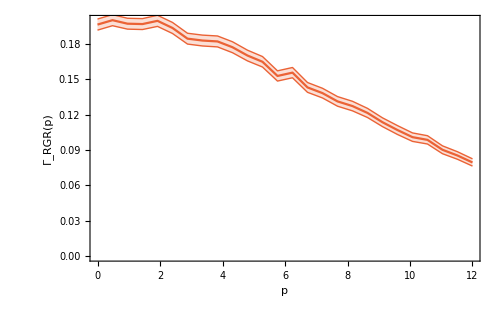

```mathematica
ListLinePlot[RGRgam,IntervalMarkers->"Bands",PlotStyle->ColorData[97,"ColorList"][[4]],PlotRange->All,Frame->True,FrameLabel->{{"Γ_RGR(p)",""},{"p","RGR marginal rate"}},FrameStyle->Directive[Black,FontSize->12],ImageSize->500]
```

```mathematica
ΓRGRtot=Sum[fBMNorm["b"]*fBM[RGRgam[[k,1]],conf["Mb"],conf["T"]]*RGRgam[[k,2]]*(RGRgam[[2,1]]-RGRgam[[1,1]]),{k,1,Length[RGRgam]}]
(*This seems reasonably uniform in γ so we'll integrate out the γ dependence*)
(*NOT SMOOTH ENOUGH*)
```

0.19350.0018

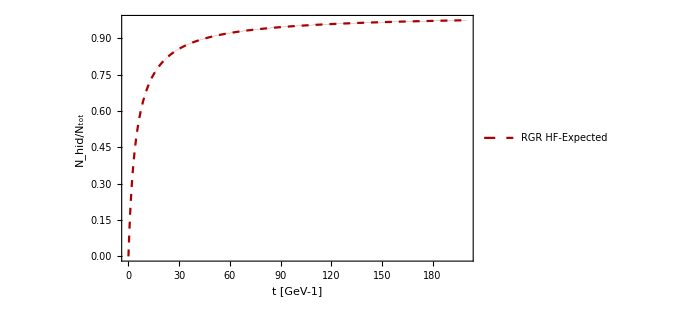

```mathematica
(*Regeneration only here, only considers Nbb*)
RGRsampHF={{0,0}};
RGRsampDist=fBMNorm["b"]*Table[fBM[pi,conf["Mb"],conf["T"]],{pi,0,conf["prCut"],0.05}];
For[i=1,i<=conf["tFn"],++i,
RGRsampDist=RGRsampDist-(RGRsampDist*((1-RGRsampHF[[-1,2]])ΓRGRtot)*conf["dt"]);(*Rate gets extra factor of (1-RGAsampHF[[-1,2]]) (1-lastHiddenFraction) reflecting the dependence on the fraction of the original (t=0) b-quark density*);
AppendTo[RGRsampHF,{i*conf["dt"],1-Total[RGRsampDist]*(conf["prCut"]/(Length[RGRsampDist]-1))}];
];
RGRExpectPlot=ListLinePlot[RGRsampHF,Frame->True,FrameLabel->{{"N_hid/N_tot",""},{"t [GeV-1]","RGR hidden fraction expectation"}},FrameStyle->Directive[Black,FontSize->12],ImageSize->500,Joined->True,PlotStyle->Directive[{Darker[Red],Dashed}],PlotLegends->{"RGR HF-Expected"}]
```

## Dissociation Momentum Sampling

### RGA Momentum Sampling

```mathematica
Bc[γ_,q_]:=γ*q/conf["T"];
Cc[r_,γ_,q_]:=(r*Log[1-Exp[-Bc[γ,q](1-vFg[γ])]])+((1-r)*Log[1-Exp[-Bc[γ,q](1+vFg[γ])]]);
CosTheta[r_,γ_,q_]:=(1/vFg[γ])*(-1-(1/Bc[γ,q])*Log[1-Exp[Cc[r,γ,q]]]);
Plot3D[CosTheta[r,1.5,q],{r,0,1},{q,conf["E1S"],conf["E1S"]*conf["ECut"]},PlotRange->All](*CosTheta^2 for visualization*)
```

-Graphics3D-

## Recombination Momentum Sampling

### RGR Momentum Sampling

### Real Gluon momentum setting

```mathematica
Fq0[pr_]:=((pr^2)/conf["Mb"])+conf["E1S"]; (* original Eq.(4.90) *)
Fq1[pr_]:=Sqrt[conf["Mb"]^2+pr^2]-((Mnl[conf["E1S"]]^2)/(4*Sqrt[conf["Mb"]^2+pr^2])); (* Strict conservation of energy *)
```

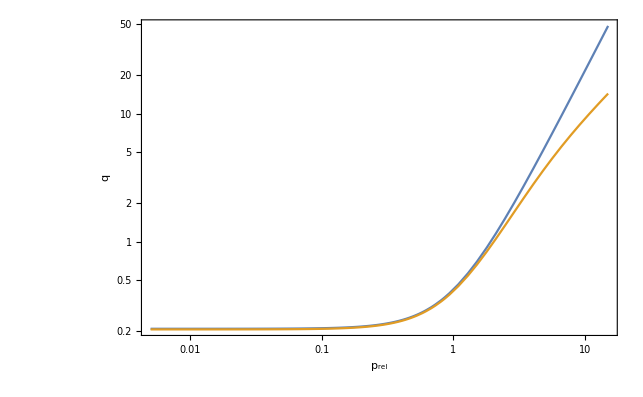

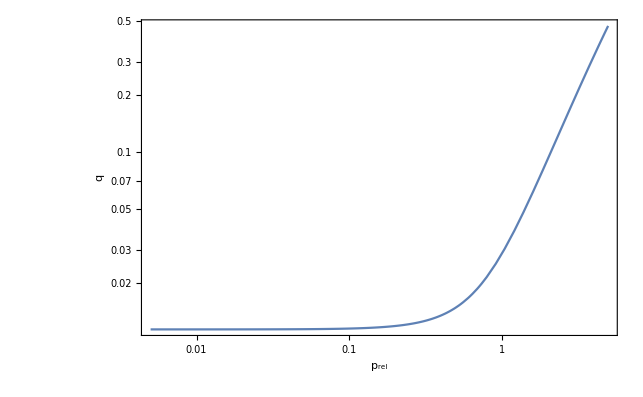

```mathematica
Fq01Plt=LogLogPlot[{Fq0[pr],Fq1[pr]},{pr,0.005,15},Frame->True,FrameLabel->{{"q",""},{"p_rel","Different q settings"}}]
Fq01RatioPlt=LogLogPlot[(Fq0[pr]/Fq1[pr])-1,{pr,0.005,5},Frame->True,FrameLabel->{{"q",""},{"p_rel","Ratio q0/q1 - 1"}}]
```

```mathematica
(*Generate prel dist*)
prC=8;
fBsamp=Interpolation[Transpose[{Table[NIntegrate[fBM[pj,conf["Mb"],conf["T"]],{pj,0,pi}],{pi,0,prC,0.005}]/NIntegrate[fBM[pn,conf["Mb"],conf["T"]],{pn,0,Infinity}],Table[pi,{pi,0,prC,0.005}]}]];
```

```mathematica
tpD=Table[Fourb[RandomPoint[Sphere[]]*fBsamp[RandomReal[]]],{i,0,200}];
```

```mathematica
Vccm0[pcm4_]:=pcm4[[2;;]]/Sqrt[(2*conf["Mb"])^2+(pcm4[[2;;]].pcm4[[2;;]])];
Vccm1[pcm4_]:=pcm4[[2;;]]/pcm4[[1]];
getprels[pSamp_,vcmType_]:=Module[{i,j,pi,pj,vcm,Bpi,Bpj,res={}},
For[i=1,i<=Length[pSamp],++i,
pi=tpD[[i]];
For[j=1,j<=Length[pSamp],++j,
If[i==j,Continue[]];
pj=tpD[[j]];
(*Boost to vcm*)
If[vcmType==0,vcm=Vccm0[pi+pj],vcm=Vccm1[pi+pj]];
{Bpi,Bpj}={Λ[vcm].pi,Λ[vcm].pj};
AppendTo[res,Norm[(Bpi[[2;;]]-Bpj[[2;;]])/2]]
];
];
res
];
```

```mathematica
{prD0,prD1}={getprels[tpD,0],getprels[tpD,1]};
```

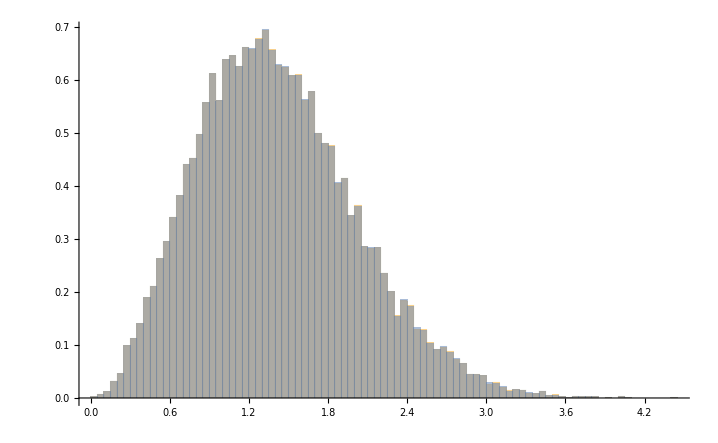

```mathematica
Histogram[{prD0,prD1},80,"PDF"]
```

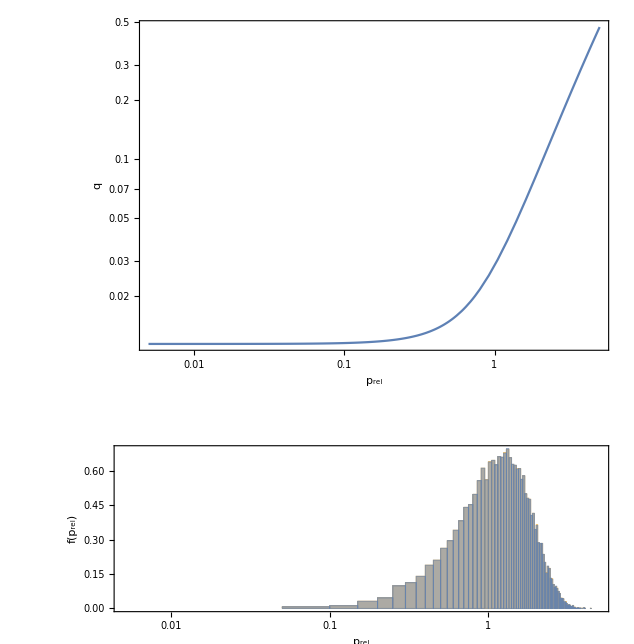

```mathematica
GraphicsColumn[{Fq01RatioPlt,Histogram[{prD0,prD1},80,"PDF",Frame->True,AspectRatio->1/4,ScalingFunctions->{"Log",None},PlotRange->{{0.005,5},All},FrameLabel->{{"f(p_rel)",""},{"p_rel","Distribution of p_rel"}}]},ImageSize->Large]
```

## Equilibrium Values

```mathematica
frel[T_,M_,g_]:=g*(conf["L"]^3)*(1/(2*Pi^2))*(M^2)*T*BesselK[2,M/T];
fnon[T_,M_,g_]:=g*(conf["L"]^3)*(M*T/(2Pi))^(3/2)*Exp[-M/T];
```

```mathematica
λrelQuad=Solve[(λ^2)*frel[conf["T"],conf["M1S"],3]+λ*frel[conf["T"],conf["Mb"],6]-(conf["NY"]+conf["Nbb"])==0,λ][[2,1,2]];
λnonQuad=Solve[(λ^2)*fnon[conf["T"],conf["M1S"],3]+λ*fnon[conf["T"],conf["Mb"],6]-(conf["NY"]+conf["Nbb"])==0,λ][[2,1,2]];
Print["λ_rel=",λrelQuad];
Print["λ_non=",λnonQuad];
```

λ_rel=293.406

λ_non=329.875

```mathematica
HFrelQ=(λrelQuad^2)*frel[conf["T"],conf["M1S"],3]/(conf["NY"]+conf["Nbb"]);
HFnonQ=(λnonQuad^2)*fnon[conf["T"],conf["M1S"],3]/(conf["NY"]+conf["Nbb"]);
```

```mathematica
Print["Relativistic Quad  N_hid/N_tot=",HFrelQ];
Print["Non-relativistic Quad  N_hid/N_tot=",HFnonQ];
Print["N_hid=",HFrelQ*(conf["NY"]+conf["Nbb"])];
```

Relativistic Quad  N_hid/N_tot=0.0000436942

Non-relativistic Quad  N_hid/N_tot=0.0000520914

N_hid=0.000218471

```mathematica
λrelLin=(conf["NY"]+conf["Nbb"])/frel[conf["T"],conf["Mb"],6]
λnonLin=(conf["NY"]+conf["Nbb"])/fnon[conf["T"],conf["Mb"],6]
```

293.419

329.892

```mathematica
HFrelL=(λrelLin^2)*frel[conf["T"],conf["M1S"],3]/(conf["NY"]+conf["Nbb"]);
HFnonL=(λnonLin^2)*fnon[conf["T"],conf["M1S"],3]/(conf["NY"]+conf["Nbb"]);
```

```mathematica
Print["Relativistic Linear  N_hid/N_tot=",HFrelL];
Print["Non-relativistic Linear  N_hid/N_tot=",HFnonL];
```

Relativistic Linear  N_hid/N_tot=0.0000436981

Non-relativistic Linear  N_hid/N_tot=0.0000520968

## Channel Approximations

### Real-Gluon Channel (RGA+RGR)

## Simulation Comparisons

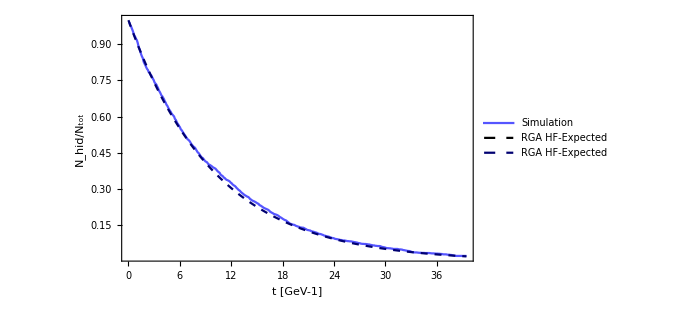

```mathematica
HFres=Import["../export/HidFrac.tsv"];
Show[ListPlot[tofm[HFres],PlotStyle->Lighter[Blue],Joined->True],RGAExpectPlot,Frame->True,FrameLabel->{{"N_hid/N_tot",""},{"t [GeV-1]","Hidden fraction comparison"}},FrameStyle->Directive[Black,FontSize->12],ImageSize->500,Joined->True,PlotStyle->Directive[{Black,Dashed}],PlotRange->All,Epilog->Inset[LineLegend[{Lighter[Blue],Directive[{Black,Dashed}]},{"Simulation","RGA HF-Expected"}],Scaled[{0.9,0.9}],{Right,Top}]]
```

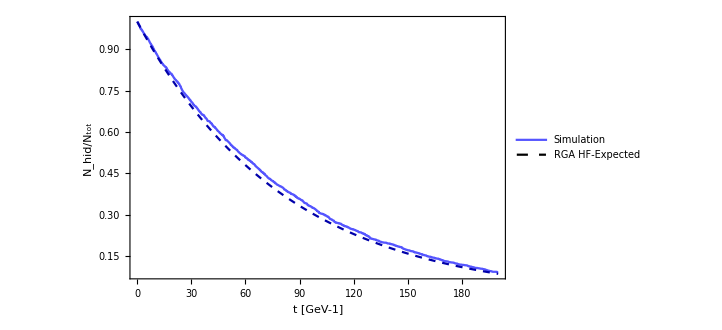
```mathematica
(*Set momentum to 10 GeV*)
-Graphics-
```

-Graphics-

-Graphics-

## Less Important Other

```mathematica
10/0.19733
```

50.6765